```mathematica
E[x_]:=Sum[  x^n/(n!*2^Binomial[n,2]),{n≥0}]
```

SetDelayed::write: Tag ⅇ in ⅇ[x_] is Protected.

$Failed

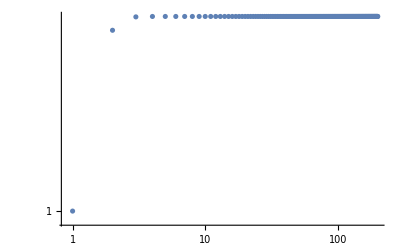

```mathematica
Table[
Sum[  x^n/(n!*2^Binomial[n,2]),{n,1,max}]/.x->1
,{max,1,200}
]//ListLogLogPlot
```

```mathematica
A[n_]:=Block[{},If[n==1,1,1-Sum[2^(k*(n-k))*Binomial[n-1,k-1]*a[k],{k,1,n-1}] ]]
```

```mathematica
Table[a[k],{k,1,13}]
```

{1,-1,5,-79,3377,-362431,93473345,-56272471039,77442176448257,-239804482525402111,1650172344732021412865,-24981899010711376986398719,825164608171793476724052668417}

```mathematica
a[1]
```

1

```mathematica
a[2]
```

-1

```mathematica
TraditionalForm[1-Sum[2^(k*(n-k))*Binomial[n-1,k-1]*AA[k],{k,1,n-1}]]
```

1-∑_(k=1)^(n-1) AA(k) 2^(k (n-k)) Binomial[n-1, k-1]

```mathematica
RecurrenceTable[{b[1]==1,b[n]==1-Sum[2^(k*(n-k))*Binomial[n-1,k-1]*b[k],{k,1,n-1}]},b,{n,1,10}]
```

RecurrenceTable::rtde: Equations b[n]==1-∑_(k=1)^(-1+n) 2^(k Plus[«2»]) b[k] Binomial[-1+n,-1+k] are not recognized as simple difference equations.

RecurrenceTable[{b[1]==1,b[n]==1-∑_(k=1)^(-1+n) 2^(k (-k+n)) b[k] Binomial[-1+n,-1+k]},b,{n,1,10}]